Gaussovo pravidlo - grafické vykreslení
Autor: David Poledne
Datum: 6. května 2025

Popis:
Tento skript graficky vykresluje uzly gaussova pravidla pro daný řád d na trojúhelníku s vrcholy vrchol1, vrchol2 , vrchol3.

Řád kvadratury: 5

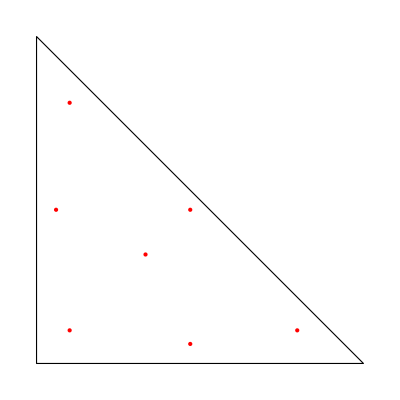

```mathematica
Remove["Global`*"]

(*Řád kvadratury *)
d=5;

(*Trojúhelník přes který se integruje*)
vrchol1={0,0};
vrchol2={1,0};
vrchol3={0,1};

Row[{"Řád kvadratury: ",d}]

(*Uzly z článku Dunavant,D.A.(1985).High degree efficient symmetrical gaussian quad-rature rules for the triangle.International journal for numerical methods in
engineering,21(6),1129–1148. *)
maxDegree=9;
degreeNodes=Table[0,{i,1,maxDegree}];
degreeNodes[[1]]={
{1.000000000000000,{ 0.333333333333333 ,0.333333333333333 ,0.333333333333333}}
};
degreeNodes[[2]]={
{0.333333333333333,{ 0.666666666666667 ,0.166666666666667 ,0.166666666666667}}
};

degreeNodes[[3]]={
{-0.562500000000000,{ 0.333333333333333 ,0.333333333333333, 0.333333333333333}},
{0.520833333333333,{0.600000000000000,0.200000000000000, 0.200000000000000}}
};
degreeNodes[[4]]={
{0.223381589678011,{ 0.108103018168070 ,0.445948490915965 ,0.445948490915965}},
{0.109951743655322 ,{0.816847572980459, 0.091576213509771, 0.091576213509771}}
};
degreeNodes[[5]]={
{0.225000000000000 ,{0.333333333333333 ,0.333333333333333, 0.333333333333333}},
{0.132394152788506,{ 0.059715871789770, 0.470142064105115 ,0.470142064105115}},
{0.125939180544827 ,{0.797426985353087, 0.101286507323456, 0.101286507323456}}
};
degreeNodes[[6]]={
{0.116786275726379 ,{0.501426509658179 ,0.249286745170910 ,0.249286745170910}},
{0.050844906370207,{ 0.873821971016996 ,0.063089014491502, 0.063089014491502}},
{0.082851075618374 ,{0.053145049844817 ,0.310352451033784, 0.636502499121399}}
};
degreeNodes[[7]]={
{-0.149570044467682 ,{0.333333333333333 ,0.333333333333333 ,0.333333333333333}},
{0.175615257433208,{ 0.479308067841920, 0.260345966079040 ,0.260345966079040}},
{0.053347235608838,{ 0.869739794195568, 0.065130102902216, 0.065130102902216}},
{0.077113760890257,{ 0.048690315425316 ,0.312865496004874 ,0.638444188569810}}
};
degreeNodes[[8]]={
{0.144315607677787 ,{0.333333333333333 ,0.333333333333333, 0.333333333333333}},
{0.095091634267285,{ 0.081414823414554, 0.459292588292723 ,0.459292588292723}},
{0.103217370534718 ,{0.658861384496480, 0.170569307751760 ,0.170569307751760}},
{0.032458497623198,{ 0.898905543365938 ,0.050547228317031 ,0.050547228317031}},
{0.027230314174435,{ 0.008394777409958 ,0.263112829634638, 0.728492392955404}}
};
degreeNodes[[9]]={
{0.097135796282799,{ 0.333333333333333, 0.333333333333333,0.333333333333333}},
{0.031334700227139,{ 0.020634961602525, 0.489682519198738,0.489682519198738}},
{0.077827541004774 ,{ 0.125820817014127 ,0.437089591492937,0.437089591492937}},
{0.079647738927210 ,{ 0.623592928761935, 0.188203535619033,0.188203535619033}},
{0.025577675658698 ,{ 0.910540973211095 ,0.044729513394453,0.044729513394453}},
{0.043283539377289 ,{ 0.036838412054736 ,0.221962989160766,0.741198598784498}}
};

permuteNode[{w_,{a_,b_,c_}}]:=Module[{perms},perms=DeleteDuplicates[Permutations[{a,b,c}]];
{w,#}&/@perms];
symmetrizedDegreeNodes=Table[Flatten[permuteNode/@degreeNodes[[d]],1],{d,1,Length[degreeNodes]}];
symmetrizedDegreeNodes=Table[DeleteDuplicatesBy[symmetrizedDegreeNodes[[d]],Last],{d,Length[symmetrizedDegreeNodes]}];
degreeNodes=symmetrizedDegreeNodes;

verticesPoints={vrchol1,vrchol2,vrchol3};

(*Převedení uzlů do kartézských souřadnic*)
s=degreeNodes[[d]];
nodes1=Table[s[[i]][[2]]={s[[i]][[2]][[1]]vrchol1[[1]]+s[[i]][[2]][[2]]vrchol2[[1]]+s[[i]][[2]][[3]]vrchol3[[1]],s[[i]][[2]][[1]]vrchol1[[2]]+s[[i]][[2]][[2]]vrchol2[[2]]+s[[i]][[2]][[3]]vrchol3[[2]]},{i,1,Length[s]}];

(*Grafické vykreslení uzlů*)
Graphics[{EdgeForm[Black],FaceForm[],Polygon[verticesPoints],Red,PointSize[Large], Point[nodes1] }]
```

```mathematica
1
```

1